abc  Integrate ∫∫ƒⅆx f∫^a ƒ(x)ⅆx  x^a

```mathematica
Integrate[f,{x,a,b}]
```

(-a+b) f

```mathematica
∫ƒ(x)ⅆx
```

```mathematica
∫
```

```mathematica
Span(x;x^2)
```

```mathematica
x;;x^2
```

x;;x^2

```mathematica
1;;4
```

1;;4

```mathematica
Total
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
weights = GaussianQuadWeights[12,-2,2];
approxint = Total[#^2[First[#]]*Last[#]&/@weights]
```

First::normal: Nonatomic expression expected at position 1 in First[12].

Last::normal: Nonatomic expression expected at position 1 in Last[12].

First::normal: Nonatomic expression expected at position 1 in First[-2].

Last::normal: Nonatomic expression expected at position 1 in Last[-2].

First::normal: Nonatomic expression expected at position 1 in First[2].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[2].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Total[GaussianQuadWeights[12^(2[First[12]]) Last[12],(-2)^(2[First[-2]]) Last[-2],2^(2[First[2]]) Last[2]]]

```mathematica
f[x_]:=Exp[x]-x^2
```

```mathematica
weights = GaussianQuadWeights[12,-2,2];
approxint = Total[f[First[#]]*Last[#]&/@weights]
```

First::normal: Nonatomic expression expected at position 1 in First[12].

Last::normal: Nonatomic expression expected at position 1 in Last[12].

First::normal: Nonatomic expression expected at position 1 in First[-2].

Last::normal: Nonatomic expression expected at position 1 in Last[-2].

First::normal: Nonatomic expression expected at position 1 in First[2].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[2].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Total[GaussianQuadWeights[(ⅇ^(First[12]^2)+First[12]^2) Last[12],(ⅇ^(First[-2]^2)+First[-2]^2) Last[-2],(ⅇ^(First[2]^2)+First[2]^2) Last[2]]]

```mathematica
weights = GaussianQuadratureWeights[12,-2,2]
```

```mathematica
weights
```

GaussianQuadWeights[12,-2,2]

```mathematica
Information[weights]
```

Information[GaussianQuadWeights[12,-2,2]]

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

GaussianQuadratureWeights::shdw: Symbol GaussianQuadratureWeights appears in multiple contexts {NumericalDifferentialEquationAnalysis`,Global`}; definitions in context NumericalDifferentialEquationAnalysis` may shadow or be shadowed by other definitions.

```mathematica
weights = GaussianQuadratureWeights[12,-2,2]
```

{{-1.96312,0.0943507},{-1.80823,0.213879},{-1.53981,0.320157},{-1.17464,0.406335},{-0.735663,0.466985},{-0.250467,0.498294},{0.250467,0.498294},{0.735663,0.466985},{1.17464,0.406335},{1.53981,0.320157},{1.80823,0.213879},{1.96312,0.0943507}}

```mathematica
weights = GaussianQuadratureWeights[12,-2,2]
approxint = Total[f[First[#]]*Last[#]&/@weights]
```

{{-1.96312,0.0943507},{-1.80823,0.213879},{-1.53981,0.320157},{-1.17464,0.406335},{-0.735663,0.466985},{-0.250467,0.498294},{0.250467,0.498294},{0.735663,0.466985},{1.17464,0.406335},{1.53981,0.320157},{1.80823,0.213879},{1.96312,0.0943507}}

27.5719

```mathematica
GaussianQuadWeights[n_,a_,b_]:=With[{ruledata=NIntegrate`GaussRuleData[n,MachinePrecision]},Transpose[{Rescale[ruledata[[1]],{0,1},{a,b}],Abs[b-a]ruledata[[2]]}]];
```

```mathematica
GaussianQuadWeights[12,-2,2]
```

{{-1.96312,0.0943507},{-1.80823,0.213879},{-1.53981,0.320157},{-1.17464,0.406335},{-0.735663,0.466985},{-0.250467,0.498294},{0.250467,0.498294},{0.735663,0.466985},{1.17464,0.406335},{1.53981,0.320157},{1.80823,0.213879},{1.96312,0.0943507}}

```mathematica
f
```

f

```mathematica
f[x]
```

ⅇ^x-x^2

```mathematica
weights = GaussianQuadratureWeights[3,-2,2]
```

{{-1.54919,1.11111},{0.,1.77778},{1.54919,1.11111}}

```mathematica
approxint = Total[f[First[#]]*Last[#]&/@weights]
```

1.91121

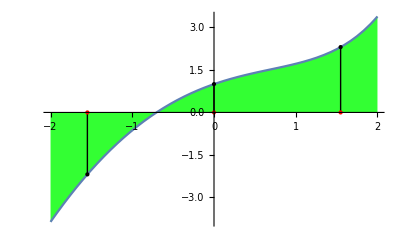

```mathematica
qp = Plot[f[x],{x,-2,2},Filling->{1->{Axis,Lighter[Green,.2]}},Epilog->{{Black,PointSize[Large],({Line[{{First[#],0},{First[#],f[First[#]]}}],Point[{First[#],f[First[#]]}]}&/@weights)},{Red,PointSize[Large],Point[{First[#],0}]&/@weights}},ImageSize->{400,400}]
```

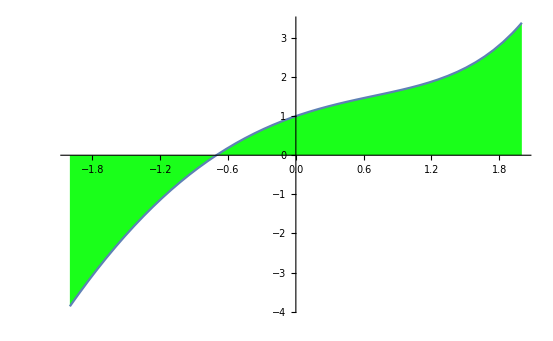

```mathematica
Plot[f[x],{x,-2,2},Filling->{1->{Axis,Lighter[Green,.1]}}]
```

```mathematica
Import["E:/sando/Pictures/"]
```

Import::fmtnosup: SVG is not a supported Import format.

$Failed

```mathematica
α=2;γ=3;
α+γ
```

5

```mathematica
n=5;h=1/n
```

1/5

```mathematica
h
```

1/5

```mathematica
h*n
```

1

```mathematica
e=ConstantArray[2,n]
```

{2,2,2,2,2}

1

```mathematica
X[ϛ_]:=1
E[x_]:=2/h*(
```

```mathematica
Product[i,{k,Select[Range[1,e[i],#≠i&]}]
```

```mathematica
{i,1,3,-2}
```

{i,1,3,-2}

```mathematica
Table[x,{x,1,-2,7}]
```

{}

```mathematica
Select[Range[1,5],#≠3&]
```

{1,2,4,5}

```mathematica
For[i=0,i≤n,i++,{
Product[i,{k,Select[Range[1,e[[i]],#≠i&]]}]
}]
```

Range::range: Range specification in Range[1,List,#1≠i&] does not have appropriate bounds.

Range::range: Range specification in Range[1,2,#1≠i&] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

```mathematica
Product[(x-(-1+2/e[i]*(k-1))),{k,Select[Range[1,e[[i]],#≠1&]]}]
```

Part::partw: Part 6 of {2,2,2,2,2} does not exist.

Range::range: Range specification in Range[1,{2,2,2,2,2}⟦6⟧,#1≠1&] does not have appropriate bounds.

Part::partw: Part 6 of {2,2,2,2,2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Range::range: Range specification in Range[1,{2,2,2,2,2}⟦6⟧,#1≠1&] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

(-2)^Select[Range[1,{2,2,2,2,2}⟦6⟧,#1≠1&]] Pochhammer[-1/2 (1+x) {2,2,2,2,2}[6],Select[Range[1,{2,2,2,2,2}⟦6⟧,#1≠1&]]] ({2,2,2,2,2}[6])^(-Select[Range[1,{2,2,2,2,2}⟦6⟧,#1≠1&]])

```mathematica
i=1
Product[(x-(-1+2/(e[[i]]-1)*(k-1))),{k,Select[Range[1,e[[i]]],#≠i&]}]
```

1

-1+x

```mathematica
i=2
Product[(x-(-1+2/(e[[i]]-1)*(k-1))),{k,Select[Range[1,e[[i]]],#≠i&]}]
```

2

1+x

```mathematica
(-1+2/e[[i]]*(k-1))
```

-2+k

```mathematica
For[i=1,i≤3,i++,{
Print[Product[(x-(-1+2/(3-1)*(k-1))),{k,Select[Range[1,3],#≠i&]}]/Product[((-1+2/(3-1)*(i-1))-(-1+2/(3-1)*(k-1))),{k,Select[Range[1,3],#≠i&]}]]
}]
```

1/2 (-1+x) x

-(-1+x) (1+x)

1/2 x (1+x)

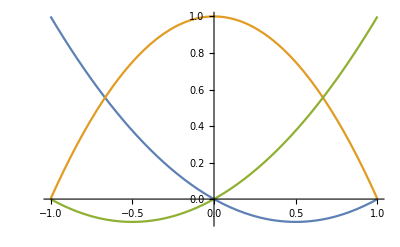

```mathematica
Plot[{1/2 (-1+x) x,-(-1+x) (1+x),1/2 x (1+x)},{x,-1,1}]
```

```mathematica
For[i=1,i≤3,i++,{
Print[Product[((-1+2/(3-1)*(i-1))-(-1+2/(3-1)*(k-1))),{k,Select[Range[1,3],#≠i&]}]]
}]
```

2

-1

2

```mathematica
InterpolatingPolynomial[{{-1,1},{0,0},{1,0}},x]
```

1+(-1+x/2) (1+x)

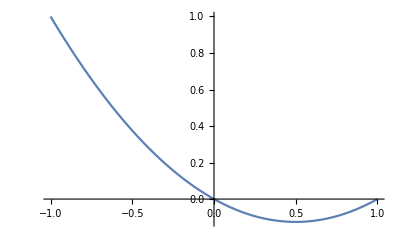

```mathematica
Plot[1+(-1+x/2) (1+x),{x,-1,1}]
```

```mathematica
InterpolatingPolynomial[{{-1,0},{0,1},{1,0}},x]
```

(1-x) (1+x)

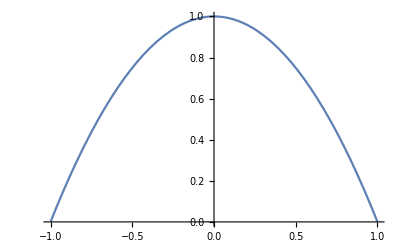

```mathematica
Plot[(1-x) (1+x),{x,-1,1}]
```

```mathematica
InterpolatingPolynomial[{{-1,0},{0,0},{1,1}},x]
```

1/2 x (1+x)

```mathematica
functionList=Table[With[{i=i},#*i*i&],{i,1,3}]

functionList[[3]][10]
```

{#1 0 0&,#1 1 1&,#1 2 2&,#1 3 3&,#1 4 4&}

40

```mathematica
fun={{InterpolatingPolynomial[{{-1,1},{1,0}},x],InterpolatingPolynomial[{{-1,0},{1,1}},x]},{InterpolatingPolynomial[{{-1,1},{0,0},{1,0}},x],InterpolatingPolynomial[{{-1,0},{0,1},{1,0}},x],InterpolatingPolynomial[{{-1,0},{0,0},{1,1}},x]}}
```

{{1+1/2 (-1-x),(1+x)/2},{1+(-1+x/2) (1+x),(1-x) (1+x),1/2 x (1+x)}}

```mathematica
fun[[1]]
```

{1+1/2 (-1-x),(1+x)/2}

```mathematica
fun[[1]][[1]]
```

1+1/2 (-1-x)

```mathematica
Plot[{fun[[2]][[1]],fun[[2]][[2]],fun[[2]][[3]]},{x,-1,1}]
```

-Graphics-

```mathematica
φ1=fun[[1]]
```

{1+1/2 (-1-x),(1+x)/2}

```mathematica
φ2=fun[[2]]
```

{1+(-1+x/2) (1+x),(1-x) (1+x),1/2 x (1+x)}

```mathematica
K1=Table[φ1[[i]]*φ1[[j]],{i,1,2},{j,1,2}]
```

{{(1+1/2 (-1-x))^2,1/2 (1+1/2 (-1-x)) (1+x)},{1/2 (1+1/2 (-1-x)) (1+x),1/4 (1+x)^2}}

```mathematica
K1//MatrixForm
```

((1+1/2 (-1-x))^2 | 1/2 (1+1/2 (-1-x)) (1+x)
1/2 (1+1/2 (-1-x)) (1+x) | 1/4 (1+x)^2)

1+1/2 (-1-x)

```mathematica
φ
```

```mathematica
InterpolatingPolynomial[{{a,1},{b,0}},x]
```

1-(-a+x)/(-a+b)

```mathematica
Simplify[1-(-a+x)/(-a+b)]
```

```mathematica
(-b+x)/(a-b)/.x->(b-a)/2*(ξ+1)+a
```

(a-b+1/2 (-a+b) (1+ξ))/(a-b)

```mathematica
Simplify[(a-b+1/2 (-a+b) (1+ξ))/(a-b)]
```

(1-ξ)/2

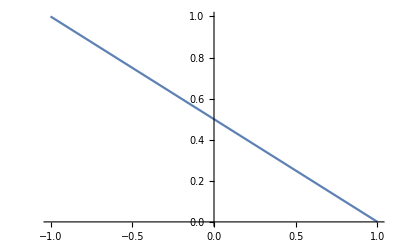

```mathematica
Plot[(1-ξ)/2,{ξ,-1,1}]
```

```mathematica
InterpolatingPolynomial[{{a,0},{a+(b-a)/2,0},{b,1}},x]
```

```mathematica
((-a+x) (-a+(a-b)/2+x))/((-a+b) (-a+(a-b)/2+b))/.x->(b-a)/2*(ξ+1)+a
```

((1+ξ) ((a-b)/2+1/2 (-a+b) (1+ξ)))/(2 (-a+(a-b)/2+b))

```mathematica
Simplify[((1+ξ) ((a-b)/2+1/2 (-a+b) (1+ξ)))/(2 (-a+(a-b)/2+b))]
```

1/2 ξ (1+ξ)

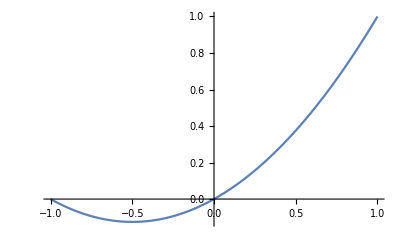

```mathematica
Plot[1/2 ξ (1+ξ),{ξ,-1,1}]
```

```mathematica
weights = GaussianQuadratureWeights[3,-2,2]
approxint = Total[f[First[#]]*Last[#]&/@weights]
GaussQ[f_,n_,a_,b_]:=Total[f[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
```

{{-1.54919,1.11111},{0.,1.77778},{1.54919,1.11111}}

1.11111 f[-1.54919]+1.77778 f[0.]+1.11111 f[1.54919]

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
GaussianQuadratureWeights[3,-2,2]
```

{{-1.54919,1.11111},{0.,1.77778},{1.54919,1.11111}}

```mathematica
GaussQ[f_,n_,a_,b_]:=Total[f[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
```

```mathematica
GaussQ[5x+Cos[9x]/.x->#&,2,-2,2]
```

-2.26935

```mathematica
Simplify[2. (-5.773502691896257-10.392304845413264 cos)+2. (5.773502691896257+10.392304845413264 cos)]
```

0.

```mathematica
Table[1,{j,1,2}{i,1,2}]
```

Table::nliter: Non-list iterator {j,1,2} {i,1,2} at position 2 does not evaluate to a real numeric value.

```mathematica
Table[i+j,{i,1,2} {j,1,2}]
```

Table::nliter: Non-list iterator {i,1,2} {j,1,2} at position 2 does not evaluate to a real numeric value.

```mathematica
Table[r+s,{r,2}, {s,2}]
```

{{2,3},{3,4}}

```mathematica
Table[i^2,{i,10},{j,10}]
```

{{1,1,1,1,1,1,1,1,1,1},{4,4,4,4,4,4,4,4,4,4},{9,9,9,9,9,9,9,9,9,9},{16,16,16,16,16,16,16,16,16,16},{25,25,25,25,25,25,25,25,25,25},{36,36,36,36,36,36,36,36,36,36},{49,49,49,49,49,49,49,49,49,49},{64,64,64,64,64,64,64,64,64,64},{81,81,81,81,81,81,81,81,81,81},{100,100,100,100,100,100,100,100,100,100}}

```mathematica
Table[i^2,{i,10},{j,10}]*2
```

{{2,2,2,2,2,2,2,2,2,2},{8,8,8,8,8,8,8,8,8,8},{18,18,18,18,18,18,18,18,18,18},{32,32,32,32,32,32,32,32,32,32},{50,50,50,50,50,50,50,50,50,50},{72,72,72,72,72,72,72,72,72,72},{98,98,98,98,98,98,98,98,98,98},{128,128,128,128,128,128,128,128,128,128},{162,162,162,162,162,162,162,162,162,162},{200,200,200,200,200,200,200,200,200,200}}

```mathematica
{
```

```mathematica
A1=Table[r+s,{r,2}, {s,2}]
```

{{2,3},{3,4}}

```mathematica
A1+A1
```

{{4,6},{6,8}}

```mathematica
{{1},{2},{3}}//MatrixForm
```

(1
2
3)

```mathematica
{{1,2,3}}//MatrixForm
```

(1 | 2 | 3)

```mathematica
For[i=1,i<m,i=i+nodes[[i]]-1,
K1[[i;;i+nodes[[i]]-1,i;;i+nodes[[i]]-1]]=K1[[i;;i+nodes[[i]]-1,i;;i+nodes[[i]]-1]]+K[[nodes[[i]]-1]]

]
```

```mathematica
For[i=1,i<m,i=i+nodes[[i]]-1,
F1[[i;;i+nodes[[i]]-1]]=F1[[i;;i+nodes[[i]]-1]]+F[[nodes[[i]]-1]]

]
```

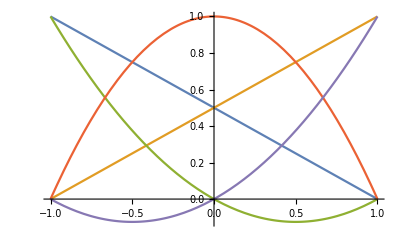

```mathematica
Plot[{{1+1/2 (-1-ξ),(1+ξ)/2},{1+(-1+ξ/2) (1+ξ),(1-ξ) (1+ξ),1/2 ξ (1+ξ)}},{ξ,-1,1}]
```